fitness

```mathematica
W[z_]:=Wmax Exp[-(z-θ)^2/2]
```

normal distribution of trait values

```mathematica
p[z_]:=PDF[NormalDistribution[μ,σ],z]
```

mean fitness

```mathematica
barW=Integrate[W[z]p[z],{z,-∞,∞},Assumptions->σ>0]
```

(ⅇ^(-(θ-μ)^2/(2 (1+σ^2))) Wmax)/(√(1+σ^2))

mean log fitness

```mathematica
FullSimplify[Log[W[z]],{Wmax>0,z>0,θ>0}];
barlogW=Integrate[%p[z],{z,-∞,∞},Assumptions->{Wmax>0,σ>0}]
```

1/2 (-(θ-μ)^2-σ^2+2 Log[Wmax])

effect of variance on relative mean fitness and mean log fitness (relative to population with no variance), at different distances to the optimum

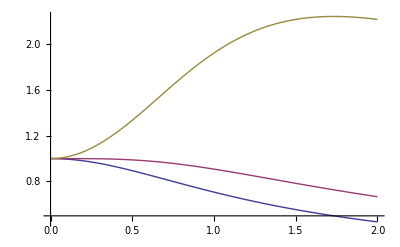

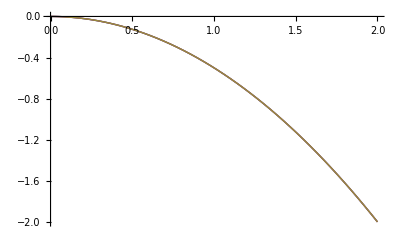

```mathematica
Wmax=1;
θ=μ+d;

barW/(barW/.σ->0)/.d->{0,1,2};
Plot[%,{σ,0,2}]

barlogW-(barlogW/.σ->0)/.d->{0,1,2};
Plot[%,{σ,0,2}]

Clear[θ,Wmax]
```

note that the effect of variance on mean fitness can be beneficial (>1) when far from the optimum and deleterious (<1) when close to the optimum. in contrast, the effect of variance on mean log fitness is invariant to distance from the optimum and always bad.